```mathematica
dir=FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"TestFiles"}]
```

/Users/john/src/chaos/TestFiles

```mathematica
f=First@FileNames[__~~"CH7"~~__~~".cdf",dir]
```

/Users/john/src/chaos/TestFiles/SW_OPER_MAGACH7_2__20220309T000000_20220309T235959_0101.cdf

```mathematica
binput=First@FileNames[__~~"LR"~~__~~".cdf",dir]
```

/Users/john/src/chaos/TestFiles/SW_OPER_MAGA_LR_1B_20220309T000000_20220309T235959_0506_MDR_MAG_LR.cdf

```mathematica
Needs["NasaCdf`"]
```

```mathematica
readNasaCdf[f,"Variables"]
```

{Timestamp,B_core_nec,B_crust_nec,B_meas_nec}

```mathematica
data=readNasaCdf[f,"Data"];
```

```mathematica
bin=readNasaCdf[binput,"Data"];
```

```mathematica
data[[1]]
```

{3.85577×10^9,{2530.19,-575.512,47444.7},{-2.59836,-0.202461,-1.95024},{2483.36,-691.841,47449.1}}

```mathematica
time=data[[All,1]];
```

```mathematica
core=data[[All,2]];
```

```mathematica
crust=data[[All,3]];
```

```mathematica
meas=data[[All,4]];
```

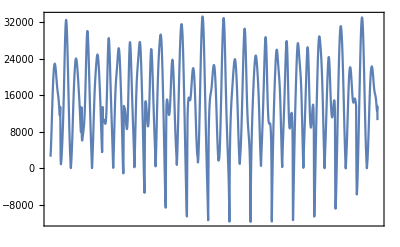

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,core[[All,1]]}],1000]]
```

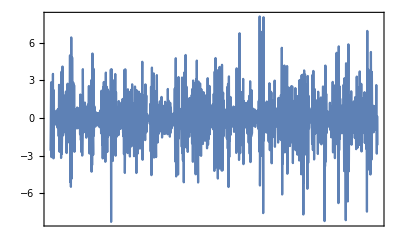

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,1]]}],1000],PlotRange->All]
```

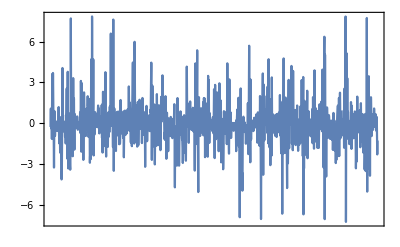

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,2]]}],1000],PlotRange->All]
```

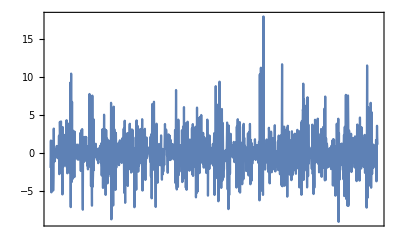

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,3]]}],1000],PlotRange->All]
```

```mathematica
StandardDeviation/@Transpose[core]
```

{9176.77,4932.93,33888.8}

```mathematica
StandardDeviation/@Transpose[crust]
```

{1.64421,1.48458,2.29024}

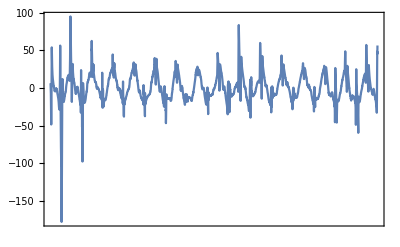

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,3]]-core[[All,3]]-crust[[All,3]]}],1000],PlotRange->All]
```

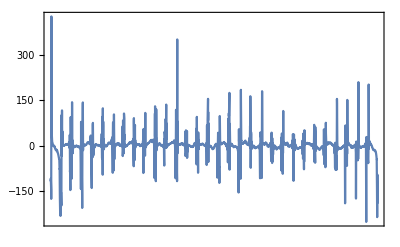

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,2]]-core[[All,2]]-crust[[All,2]]}],1000],PlotRange->All]
```

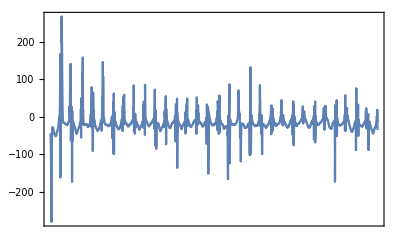

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,1]]-core[[All,1]]-crust[[All,1]]}],1000],PlotRange->All]
```

```mathematica
ind=1;;3000;
```

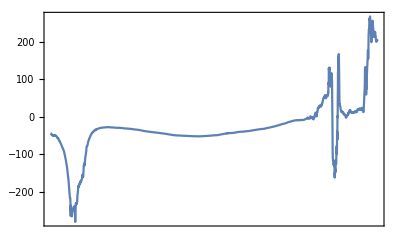

```mathematica
DateListPlot[Transpose[{time[[ind]],meas[[ind,1]]-core[[ind,1]]-crust[[ind,1]]}],PlotRange->All]
```

```mathematica
ind=650;;3000;
```

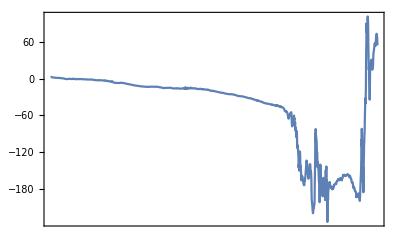

```mathematica
DateListPlot[Transpose[{time[[ind]],meas[[ind,2]]-core[[ind,2]]-crust[[ind,2]]}],PlotRange->All]
```

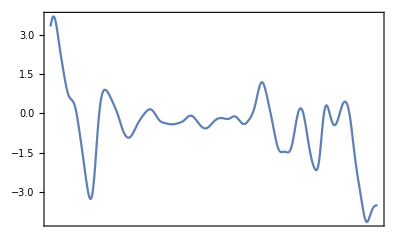

```mathematica
DateListPlot[Transpose[{time[[ind]],crust[[ind,2]]}],PlotRange->All]
```

```mathematica
DateList@time[[ind]][[1]]
```

{2022,3,9,0,10,49.}

```mathematica
DateDifference[{2022},time[[ind]][[1]]]
```

67.0075 days

```mathematica
fr=2022+67.0075/365.25
```

```mathematica
2022.1834565366187
```

```mathematica
crust[[1]]
```

{-2.59836,-0.202461,-1.95024}

This is the same output as the matlab CHAOS example, to two decimal places, modified to show crustal model, which uses the order 6 BSpline. Validates crustal field implemented correctly.

```mathematica
readNasaCdf[binput,"Variables"]
```

{Timestamp,SyncStatus,Latitude,Longitude,Radius,F,dF_AOCS,dF_other,F_error,B_VFM,B_NEC,dB_Sun,dB_AOCS,dB_other,B_error,q_NEC_CRF,Att_error,Flags_F,Flags_B,Flags_q,Flags_Platform,ASM_Freq_Dev}

```mathematica
bin[[1]]
```

{3.85577×10^9,0,76.0051,-96.2096,6.79336×10^6,0.,0.1575,-0.0134,0.,{45550.4,2568.62,13290.},{2483.36,-691.841,47449.1},{0.7156,0.3889,1.6205},{-0.3316,0.0113,1.635},{-0.1884,0.0137,-0.0436},{0.2138,0.2153,0.3116},{-0.00325244,-0.000321896,-0.995969,0.0896356},1.1492,255,8,0,1,0.}

```mathematica
DateDifference[{2000},time[[1]]]
```

8103. days

```mathematica
90-76.0051
```

13.9949

```mathematica
alt=bin[[1,5]]/1000.-6371.2
```

422.158